### Ejercicio 1: Encontrar distribución de ajuste

#### Generar data

Primero generaremos data random de una distribución

```mathematica
data=RandomVariate[GumbelDistribution[5,1.5],200];
```

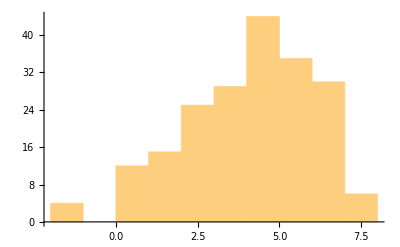

```mathematica
Histogram[data]
```

#### Método Jack-Knife

```mathematica
jackdata=Table[Drop[data,{k}],{k,Length@data}];
```

```mathematica
Dimensions@jackdata
```

{200,199}

```mathematica
AbsoluteTiming[solsk=FindMaximum[LogLikelihood[NormalDistribution[u,s],#],{u,s}]& /@ jackdata;//Quiet]
```

{1.54543,Null}

```mathematica
ues=solsk[[All,2,1,2]];
ses=solsk[[All,2,2,2]];
```

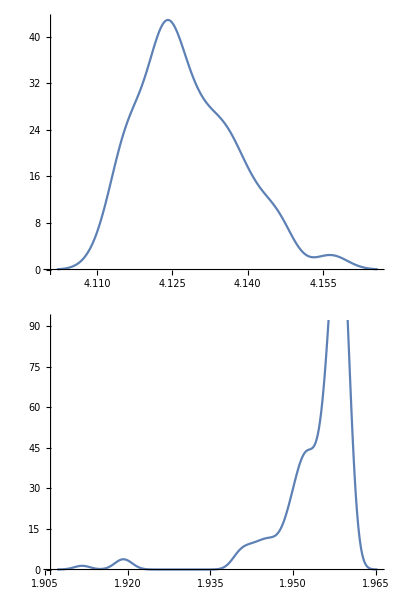

```mathematica
SmoothHistogram[#]&/@{ues,ses}//TableForm
```

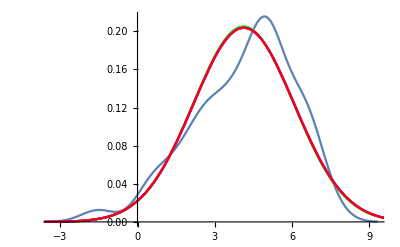

```mathematica
Show[
SmoothHistogram[data],
Table[Plot[
PDF[NormalDistribution[ues[[30n]],ses[[30n]]],x],{x,-6,10},PlotStyle->Hue[n/6]],{n,1,6}]
]
```

```mathematica
Quantile[ues,{0.025,0.975}]
```

{4.11303,4.14754}

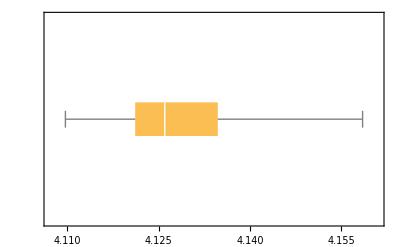

```mathematica
BoxWhiskerChart[ues,BarOrigin->Left]
```

```mathematica
Quantile[ses,{0.025,0.975}]
```

{1.93994,1.95935}

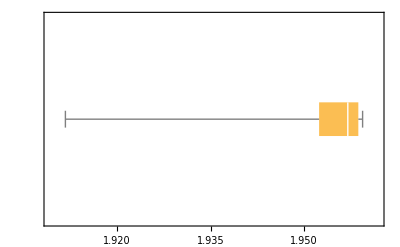

```mathematica
BoxWhiskerChart[ses,BarOrigin->Left]
```

#### Bootstrap

```mathematica
bootdata=RandomChoice[data,{1000,200}];
```

```mathematica
AbsoluteTiming[sols=FindMaximum[LogLikelihood[NormalDistribution[μ,σ],#],{{μ,4.37},{σ,1.77}},Method->"Newton"]& /@ bootdata;//Quiet]
```

{5.91372,Null}

```mathematica
mues=μ/.sols[[All,2]];
sigs=σ/.sols[[All,2]];
```

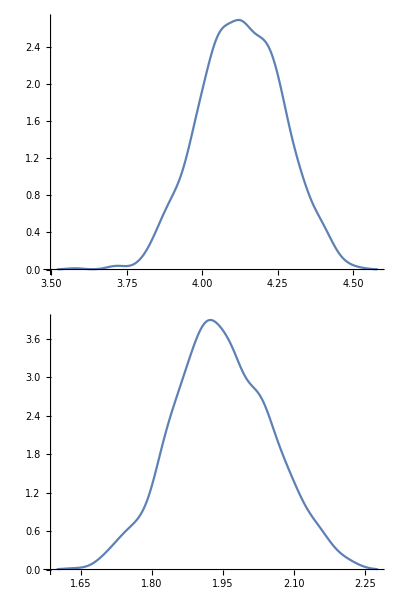

```mathematica
SmoothHistogram[#]&/@{mues,sigs}//TableForm
```

```mathematica
Quantile[mues,{0.025,0.975}]
```

{3.86537,4.38902}

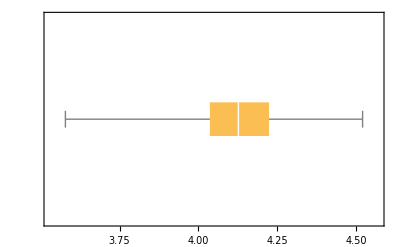

```mathematica
BoxWhiskerChart[mues,BarOrigin->Left]
```

```mathematica
Quantile[sigs,{0.025,0.975}]
```

{1.74889,2.15278}

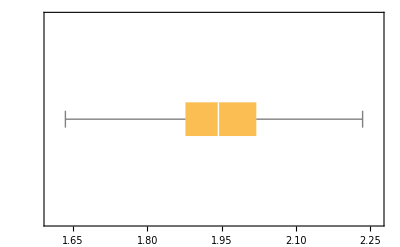

```mathematica
BoxWhiskerChart[sigs,BarOrigin->Left]
```

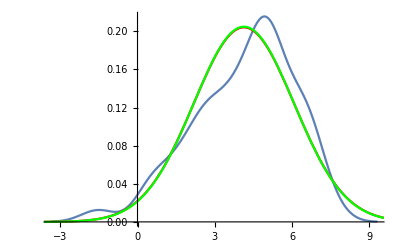

```mathematica
Show[
SmoothHistogram[data],
Plot[PDF[NormalDistribution[Mean[ues],Mean[ses]],x],{x,-6,10},PlotStyle->Red],
Plot[PDF[NormalDistribution[Mean[mues],Mean[sigs]],x],{x,-6,10},PlotStyle->Green]
]
```

## Ejercicio 2: Regularización

Ahora, generemos una serie de datos correlacionados, en este caso, una señal de seno multiplicada por la suma de cosenos de distintas frecuencias modulados por números random entre 0 y 2. Con ruido que varia entre el maximo y el mínimo de la señal original partido por 5.

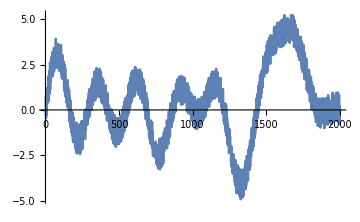

```mathematica
n = 2000;
times = N[Range[0,n-1,1]];
original=Sin[2Pi times/n]Sum[RandomInteger[{0,2}]Cos[times m 0.001],{m,1,20}];
corrupted = original + RandomReal[{Min[original]/5,Max[original]/5},n];
ListLinePlot[corrupted,ImageSize->Medium]
```

```mathematica
id=IdentityMatrix[n];
recovered=Table[Fit[{id,corrupted},"BestFitParameters",FitRegularization->{"Variation",n}],{n,1,501,50}]
```

{{0.381466,-0.0222327,-0.196496,-0.224917,-0.021675,1991,-0.220436,-0.148034,-0.458957,-0.637842},10}
 |  |  |  |

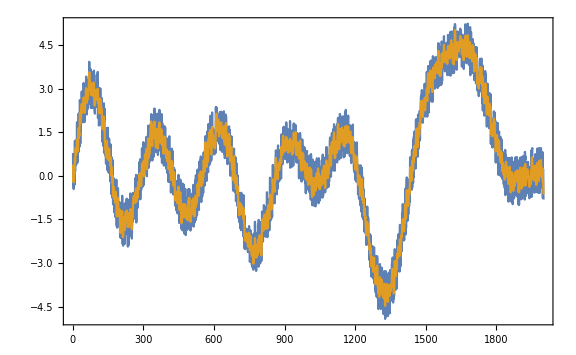
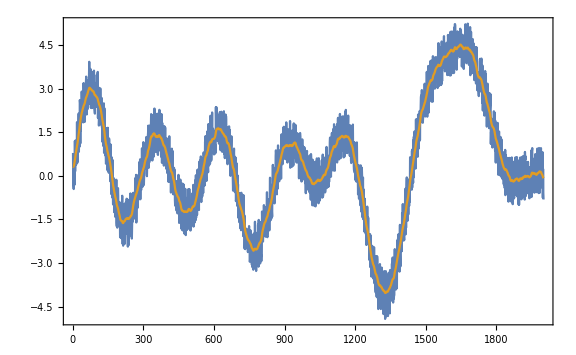
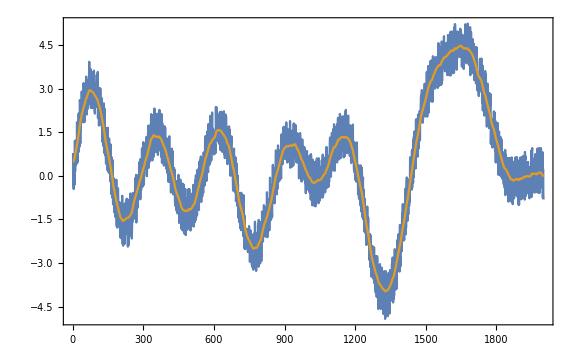
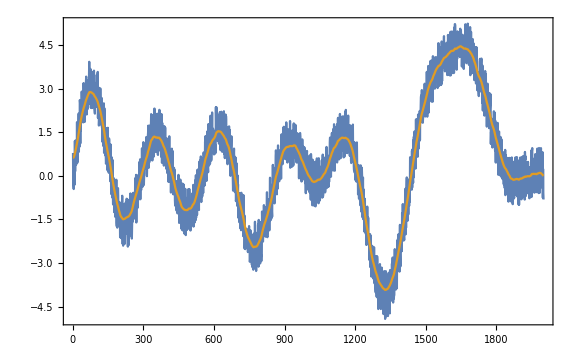
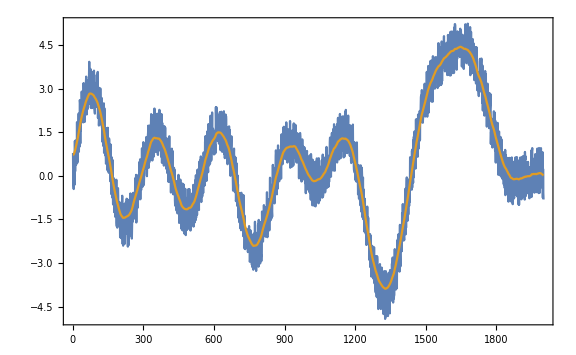
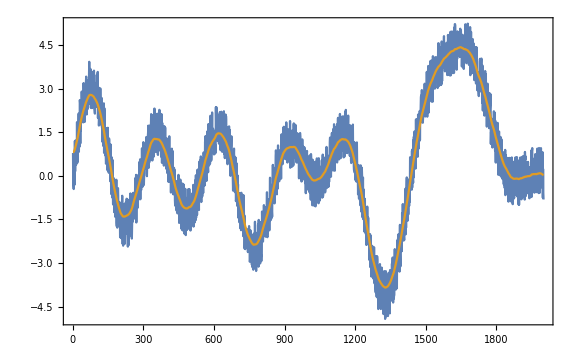
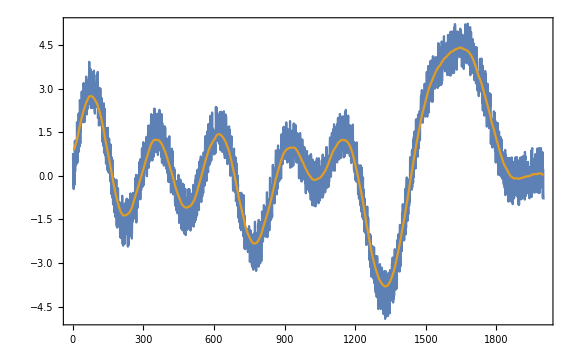
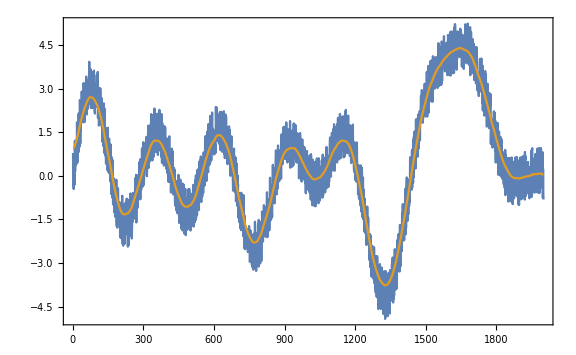

```mathematica
Table[ListLinePlot[{ corrupted,recovered[[n]]},Frame->True,ImageSize->Large],{n,1,Length@recovered}]
```

Para conseguir el λ óptimo, utilizamos la curva de variación de λ:

```mathematica
lcurveVariation = Table[{smoothed, residual} = Fit[{id,corrupted},{"BestFitParameters","FitResiduals"},FitRegularization->{"Variation",2^logλ}];Tooltip[{Norm[residual],Norm[Differences[smoothed]]},2.^logλ],{logλ,-5,20}];
```

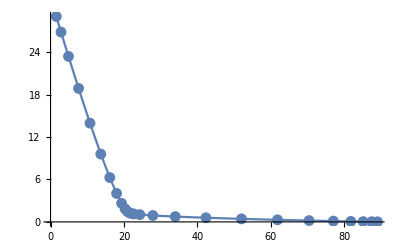

```mathematica
ListLinePlot[lcurveVariation,Joined->True,Mesh->All]
```

Viendo que hay varios valores cercanos el uno al otro en la “esquina” que buscamos, volvemos a hacer el gráfico, con valores de logλ más acotados.

```mathematica
lcurveVariation2 = Table[{smoothed, residual} = Fit[{id,corrupted},{"BestFitParameters","FitResiduals"},FitRegularization->{"Variation",2^logλ}];Tooltip[{Norm[residual],Norm[Differences[smoothed]]},2.^logλ],{logλ,2,10}];
```

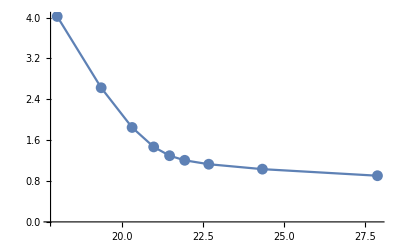

```mathematica
ListLinePlot[lcurveVariation2,Joined->True,Mesh->All]
```

Elegimos uno de los valores aproximadamente más cercanos a la “esquina” (hay que recordar que esta es una regla al ojo, no es exacta y debemos tomar decisiones)

```mathematica
recovered2=Fit[{id,corrupted},"BestFitParameters",FitRegularization->{"Variation",256}];
```

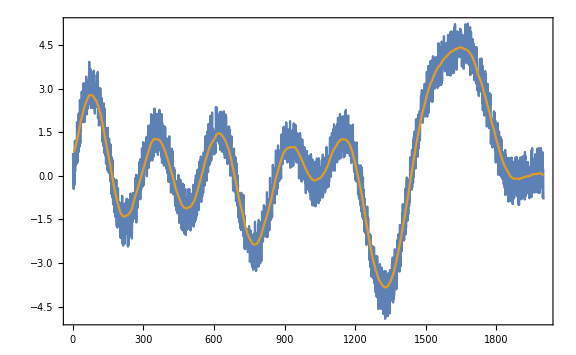

```mathematica
ListLinePlot[{ corrupted,recovered2},Frame->True,ImageSize->Large]
```